# Solving k-essence background evolution ODE

## Parameters

```mathematica
Xhat=8;
g0=0.0;
g2=1.0;
g4=1 10^-12;
```

## Definitions:

```mathematica
X = 1/(2 a[τ]^2)(ϕ'[τ]^2-(D[ϕ[τ], x])^2);
K = -g0+g2(X-Xhat)^2+g4(X-Xhat)^4;
Subscript[K, X]=2.0g2(X-Xhat)+4.0g4(X-Xhat)^3;
Subscript[K, XX] = 2 g2 +12 g4 (X-Xhat)^2;
Subscript[K, ϕ]=0;
Subscript[K, ϕX]=0;
cs2 = Subscript[K, X]/(2X Subscript[K, XX]+Subscript[K, X]);
```

## Functions

```mathematica
scalfactor[z_]:=1/(1+z);
redshift[a_]:=1/a-1;
(*Function to compute conformal time for a given redshift*)
tau[zs_,H0_,Ωm_,Ωd_,w_,Ωr_]:=NIntegrate[H0^-1/(√(Ωd(1+z)^(3(1+w)) +Ωm (1+z)^3+Ωr(1+z)^4)),{z,zs,∞},PrecisionGoal->12,AccuracyGoal->12]
(*Conformal Hubble Function at a given redshift *)
ConformalHubble[z_,H0_,Ωm_,Ωd_,w_,Ωr_]:=H0 √(Ωd(1+z)^(1+3 w) +Ωm (1+z)+Ωr(1+z)^2)
```

## Cosmological components

```mathematica
w = -1.0;
H0=0.0691023 (*time is measured in Giga year*);
Ωm=0.31;
ΩR=9 10^-5;
Ωd=1-Ωm-ΩR;
```

## ODEs

```mathematica
ODE = (Subscript[K, X]+ ϕ'[τ]^2/a[τ]^2 Subscript[K, XX])ϕ''[τ] - a[τ]^2(Subscript[K, ϕ] - ϕ'[τ]^2/a[τ]^2 Subscript[K, ϕX]) + a'[τ]/a[τ](2 Subscript[K, X] -  ϕ'[τ]^2/a[τ]^2 Subscript[K, XX])ϕ'[τ] + Subscript[K, X] D[ϕ[τ], x,x] + Subscript[K, ϕX] D[ϕ[τ], x]D[ϕ[τ], x] +2 Subscript[K, XX]/a[τ]^2 ϕ'[τ]D[ϕ[τ], x]D[ϕ[τ], x,τ]- a'[τ]/a[τ] Subscript[K, XX]/a[τ]^2 ϕ'[τ]D[ϕ[τ], x]D[ϕ[τ], x]- Subscript[K, XX]/a[τ]^2 D[ϕ[τ], x]D[ϕ[τ], x] D[ϕ[τ], x,x];
ODEa = a'[τ] -a[τ]H0 √(ΩR a[τ]^-2 + Ωm a[τ]^-1+(1-Ωm)a[τ]^(-(1+3 w)));
```

## Initial conditions

```mathematica
τini = tau[100,H0,Ωm,Ωd,w,ΩR];
τfin= tau[0,H0,Ωm,Ωd,w,ΩR];
ϕini =0.00451695/H0 (*ϕ [CLASS] H0[CLASS]/H0[our units here]*); 
ϕfin =3.67315676/H0 (*ϕ [CLASS] H0[CLASS]/H0[our units here]*); 
ϕpini=0.03960485908790306;
ϕpfin=4.000000000052;
Print[[ϕini,ϕfin ]]
```

Print⟦0.0653661,53.1553⟧

```mathematica
τfin
```

46.3205

```mathematica
τini
```

4.36201

## ODEs solution

```mathematica
(*s=NDSolve[{ODEa==0,ODE==0,a[τfin]==1.0,ϕ[τfin]==ϕfin, ϕ'[τfin]==ϕpfin},{a[τ],a'[τ],ϕ[τ],ϕ'[τ]},{τ,τini,τfin}]*)
```

```mathematica
sfin=NDSolve[{ODEa==0,ODE==0,a[τfin]==1.0,ϕ[τfin]==ϕfin, ϕ'[τfin]==ϕpfin},{a[τ],a'[τ],ϕ[τ],ϕ'[τ]},{τ,τini,τfin},Method->{"ExplicitRungeKutta"}]
```

{{a[τ]→InterpolatingFunction[…][τ],a'[τ]→InterpolatingFunction[…][τ],ϕ[τ]→InterpolatingFunction[…][τ],ϕ'[τ]→InterpolatingFunction[…][τ]}}

```mathematica
(*sini=NDSolve[{ODEa==0,ODE==0,a[τfin]==1.0,ϕ[τfin]==ϕini, ϕ'[τfin]==ϕpini},{a[τ],a'[τ],ϕ[τ],ϕ'[τ]},{τ,τini,τfin},Method->{"Midpoint"}]
*)
sini = NDSolve[{ODEa==0,ODE==0,a[τfin]==1.0,ϕ[τini]==ϕini, ϕ'[τini]==ϕpini},{a[τ],a'[τ],ϕ[τ],ϕ'[τ]},{τ,τini,τfin},Method->{"ExplicitRungeKutta"}](* Method->PIERK*)
```

{{a[τ]→InterpolatingFunction[…][τ],a'[τ]→InterpolatingFunction[…][τ],ϕ[τ]→InterpolatingFunction[…][τ],ϕ'[τ]→InterpolatingFunction[…][τ]}}

### Comparing Values

#### hiclass values

```mathematica
(*hiclass values!*)
(*print("hiclass, z=100: ",phi_smg(100.0)*H0,phi_prime(100.0))
print("hiclass, z=90: ",phi_smg(90.0)*H0,phi_prime(90.0))
print("hiclass, z=0: ",phi_smg(0.0)*H0,phi_prime(0.0))
*)
(*('hiclass,z=100:',array([0.00451695]),array(0.03960485908790306))
('hiclass,z=90:',array([0.00525347]),array(0.04395695258194529))
('hiclass,z=0:',array([3.67315676]),array(4.000000000052))*)
```

#### k-evolution values

```mathematica
ϕkevolution = {{100,0.00451688,0.0397365},{90,0.004575818400044167,0.0401200149119417}}
```

{{100,0.00451688,0.0397365},{90,0.00457582,0.04012}}

```mathematica
(*print(" gev: z=100",phi_gev(100),phi_prime_gev(100))
print("gev: z=90",phi_gev(90.),phi_prime_gev(90.))
print("gev: z=0",phi_gev(0),phi_prime_gev(0))*)
(*(' gev:z=100',array(0.00451688),array(0.0397365))
('gev:z=90',array(0.004575818400044167),array(0.0401200149119417))
('gev:z=0',array(nan),array(nan))*)
```

```mathematica
(*('hiclass,z=100:',array([0.00451695]),array(0.03960485908790306))
('hiclass,z=90:',array([0.00525347]),array(0.04395695258194529))
('hiclass,z=10:',array([0.12226659]),array(0.3636372307636966))
('hiclass,z=0:',array([3.67315676]),array(4.000000000052))
(' gev:z=100',array(0.00451688),array(0.039621))
('gev:z=90',array(0.004575400889523391),array(0.04002031825170218))
('gev:z=10',array(0.010726074977168949),array(0.22674614611872146))
('gev:z=0',array(0.20177239302875022),array(2.493840068203949))*)
```

#### Mathematics values

```mathematica
ϕMathematica[τ_] := Evaluate[{ϕ[τ]*H0/.sini,ϕ[τ]*H0/.sfin }]
ϕprimeMathematica[τ_] := Evaluate[{ϕ'[τ]/.sini,ϕ'[τ]/.sfin }]
Print["phi_smg * H0 (z=100):",ϕMathematica[τini]]
Print["phi_smg * H0 (z=90):",ϕMathematica[ tau[90,H0,Ωm,Ωd,w,ΩR]]]
Print["phi_smg * H0 (z=10):",ϕMathematica[ tau[10,H0,Ωm,Ωd,w,ΩR]]]
Print["phi_smg * H0 (z=0):",ϕMathematica[ tau[0,H0,Ωm,Ωd,w,ΩR]]]
```

phi_smg * H0 (z=100):{0.0691023 ϕ[4.36201]/.NDSolve[{-0.0691023 a[4.36201] √(9/(100000 a[4.36201]^2)+0.31/a[4.36201]+0.69 a[4.36201]^2.)+a'[4.36201]==0,(a'[4.36201] ϕ'[4.36201] (-(ϕ'[4.36201]^2 (2.+(3 (-8+ϕ'[4.36201]^2/(2 a[4.36201]^2))^2)/250000000000))/a[4.36201]^2+2 (2. (-8+ϕ'[4.36201]^2/(2 a[4.36201]^2))+4.×10^-12 (-8+ϕ'[4.36201]^2/(2 a[4.36201]^2))^3)))/a[4.36201]+(2. (-8+ϕ'[4.36201]^2/(2 a[4.36201]^2))+4.×10^-12 (-8+ϕ'[4.36201]^2/(2 a[4.36201]^2))^3+(ϕ'[4.36201]^2 (2.+(3 (-8+ϕ'[4.36201]^2/(2 a[4.36201]^2))^2)/250000000000))/a[4.36201]^2) ϕ''[4.36201]==0,a[46.3205]==1.,ϕ[4.36201]==0.0653661,ϕ'[4.36201]==0.0396049},{a[4.36201],a'[4.36201],ϕ[4.36201],ϕ'[4.36201]},{4.36201,4.36201,46.3205},Method→{ExplicitRungeKutta}],{-0.141797}}

phi_smg * H0 (z=90):{0.0691023 ϕ[4.63503]/.NDSolve[{-0.0691023 a[4.63503] √(9/(100000 a[4.63503]^2)+0.31/a[4.63503]+0.69 a[4.63503]^2.)+a'[4.63503]==0,(a'[4.63503] ϕ'[4.63503] (-(ϕ'[4.63503]^2 (2.+(3 (-8+ϕ'[4.63503]^2/(2 a[4.63503]^2))^2)/250000000000))/a[4.63503]^2+2 (2. (-8+ϕ'[4.63503]^2/(2 a[4.63503]^2))+4.×10^-12 (-8+ϕ'[4.63503]^2/(2 a[4.63503]^2))^3)))/a[4.63503]+(2. (-8+ϕ'[4.63503]^2/(2 a[4.63503]^2))+4.×10^-12 (-8+ϕ'[4.63503]^2/(2 a[4.63503]^2))^3+(ϕ'[4.63503]^2 (2.+(3 (-8+ϕ'[4.63503]^2/(2 a[4.63503]^2))^2)/250000000000))/a[4.63503]^2) ϕ''[4.63503]==0,a[46.3205]==1.,ϕ[4.36201]==0.0653661,ϕ'[4.36201]==0.0396049},{a[4.63503],a'[4.63503],ϕ[4.63503],ϕ'[4.63503]},{4.63503,4.36201,46.3205},Method→{ExplicitRungeKutta}],{-0.141009}}

phi_smg * H0 (z=10):{0.0691023 ϕ[14.8107]/.NDSolve[{-0.0691023 a[14.8107] √(9/(100000 a[14.8107]^2)+0.31/a[14.8107]+0.69 a[14.8107]^2.)+a'[14.8107]==0,(a'[14.8107] ϕ'[14.8107] (-(ϕ'[14.8107]^2 (2.+(3 (-8+ϕ'[14.8107]^2/(2 a[14.8107]^2))^2)/250000000000))/a[14.8107]^2+2 (2. (-8+ϕ'[14.8107]^2/(2 a[14.8107]^2))+4.×10^-12 (-8+ϕ'[14.8107]^2/(2 a[14.8107]^2))^3)))/a[14.8107]+(2. (-8+ϕ'[14.8107]^2/(2 a[14.8107]^2))+4.×10^-12 (-8+ϕ'[14.8107]^2/(2 a[14.8107]^2))^3+(ϕ'[14.8107]^2 (2.+(3 (-8+ϕ'[14.8107]^2/(2 a[14.8107]^2))^2)/250000000000))/a[14.8107]^2) ϕ''[14.8107]==0,a[46.3205]==1.,ϕ[4.36201]==0.0653661,ϕ'[4.36201]==0.0396049},{a[14.8107],a'[14.8107],ϕ[14.8107],ϕ'[14.8107]},{14.8107,4.36201,46.3205},Method→{ExplicitRungeKutta}],{-0.0156987}}

phi_smg * H0 (z=0):{0.0691023 ϕ[46.3205]/.NDSolve[{-0.0691023 a[46.3205] √(9/(100000 a[46.3205]^2)+0.31/a[46.3205]+0.69 a[46.3205]^2.)+a'[46.3205]==0,(a'[46.3205] ϕ'[46.3205] (-(ϕ'[46.3205]^2 (2.+(3 (-8+ϕ'[46.3205]^2/(2 a[46.3205]^2))^2)/250000000000))/a[46.3205]^2+2 (2. (-8+ϕ'[46.3205]^2/(2 a[46.3205]^2))+4.×10^-12 (-8+ϕ'[46.3205]^2/(2 a[46.3205]^2))^3)))/a[46.3205]+(2. (-8+ϕ'[46.3205]^2/(2 a[46.3205]^2))+4.×10^-12 (-8+ϕ'[46.3205]^2/(2 a[46.3205]^2))^3+(ϕ'[46.3205]^2 (2.+(3 (-8+ϕ'[46.3205]^2/(2 a[46.3205]^2))^2)/250000000000))/a[46.3205]^2) ϕ''[46.3205]==0,a[46.3205]==1.,ϕ[4.36201]==0.0653661,ϕ'[4.36201]==0.0396049},{a[46.3205],a'[46.3205],ϕ[46.3205],ϕ'[46.3205]},{46.3205,4.36201,46.3205},Method→{ExplicitRungeKutta}],{3.67316}}

```mathematica
Print["phi'_smg (z=100):",ϕprimeMathematica[τini]]
Print["phi'_smg  (z=90):",ϕprimeMathematica[ tau[90,H0,Ωm,Ωd,w,ΩR]]]
Print["phi'_smg  (z=10):",ϕprimeMathematica[ tau[10,H0,Ωm,Ωd,w,ΩR]]]
Print["phi'_smg (z=0):",ϕprimeMathematica[ tau[0,H0,Ωm,Ωd,w,ΩR]]]
```

phi'_smg (z=100):{{0.000108204},{5.40699}}

phi'_smg  (z=90):{{0.00013329},{5.38188}}

phi'_smg  (z=10):{{0.00913819},{5.32507}}

phi'_smg (z=0):{{1.70561},{4.}}

```mathematica
Print["phi_smg * H0 (z=100):",ϕMathematica[τini]]
Print["phi_smg * H0 (z=90):",ϕMathematica[ tau[90,H0,Ωm,Ωd,w,ΩR]]]
Print["phi_smg * H0 (z=10):",ϕMathematica[ tau[10,H0,Ωm,Ωd,w,ΩR]]]
Print["phi_smg * H0 (z=0):",ϕMathematica[ tau[0,H0,Ωm,Ωd,w,ΩR]]]
```

phi_smg * H0 (z=100):{{0.004523},{-11.1945}}

phi_smg * H0 (z=90):{{0.00452527},{-11.0928}}

phi_smg * H0 (z=10):{{0.00648727},{-7.34175}}

phi_smg * H0 (z=0):{{0.69695},{3.67316}}

## Figures

```mathematica
plt = Plot[Evaluate[{a[τ],a'[τ]}/.s],{τ,τini,τfin},PlotRange->Full,PlotLegends->{"a[τ]","a'[τ]"}, PlotStyle->{Red,Black,Thick}, ImageSize->600,AxesLabel->{"...","τ"}];
plt2 = Plot[Evaluate[{ϕ[τ],ϕ'[τ]}/.s],{τ,τini,τfin},PlotRange->Full,PlotLegends->{"ϕ[τ]","ϕ'[τ]"}, PlotStyle->Thick, ImageSize->600,AxesLabel->{"...","τ"}];
Show[plt,plt2]
```

-Graphics-

### Table -- Plotting as a function of redshift

```mathematica
dataHubble = Table[{Evaluate[(1/a[τ])/.sfin],Evaluate[a'[τ]/a[τ]/.sfin]},{τ,τini,τfin,0.01}];
dataϕsfin = Table[{Evaluate[(1/a[τ])/.sfin],Evaluate[ϕ[τ]*H0/.sfin]},{τ,τini,τfin,0.01}];
dataϕprimesfin = Table[{Evaluate[(1/a[τ])/.sfin],Evaluate[ϕ'[τ]/.sfin]},{τ,τini,τfin,0.01}];
dataϕsini = Table[{Evaluate[(1/a[τ])/.sini],Evaluate[ϕ[τ]*H0/.sini]},{τ,τini,τfin,0.01}];
dataϕprimesini = Table[{Evaluate[(1/a[τ])/.sini],Evaluate[ϕ'[τ]/.sini]},{τ,τini,τfin,0.01}];
```

### Plots

```mathematica
PlotHubble = ListLogLogPlot[dataHubble[[All,{1,2},1]],PlotStyle->Red,Joined->True,PlotRange->Full,PlotLegends->{"Η[τ]"}, PlotStyle->Thick, ImageSize->600,AxesLabel->{Style["1+z",FontSize->30],Style["1+z",FontSize->30]}];
Plotϕini = ListLogLogPlot[dataϕsini[[All,{1,2},1]],PlotStyle->Red,Joined->True,PlotRange->{{1,100},{10^-3,10}},PlotLegends->{"ϕ[τ](initial values given)"}, PlotStyle->Thick, ImageSize->600,AxesLabel->{Style["1+z",Purple,FontSize->30]}];
Plotϕfin = ListLogLogPlot[dataϕsfin[[All,{1,2},1]],PlotStyle->Blue,Joined->True,PlotRange->{{1,100},{10^-3,10}},PlotLegends->{"ϕ[τ](final values given)"}, PlotStyle->Thick, ImageSize->600,AxesLabel->{Style["1+z",Purple,FontSize->30]}];
Plotϕprimeini = ListLogLogPlot[dataϕprimesini[[All,{1,2},1]],PlotStyle->{Purple,Thick},Joined->True,PlotRange->{{1,100},{10^-3,10}},PlotLegends->{"ϕ'[τ](initial values given)"}, ImageSize->600,AxesLabel->{Style["1+z",Blue,FontSize->30]}];
Plotϕprimefin = ListLogLogPlot[dataϕprimesfin[[All,{1,2},1]],PlotStyle->{Green,Thick},Joined->True,PlotRange->{{1,100},{10^-3,10}},PlotLegends->{"ϕ'[τ](final values given)"}, ImageSize->600,AxesLabel->{Style["1+z",Blue,FontSize->30]}];
```

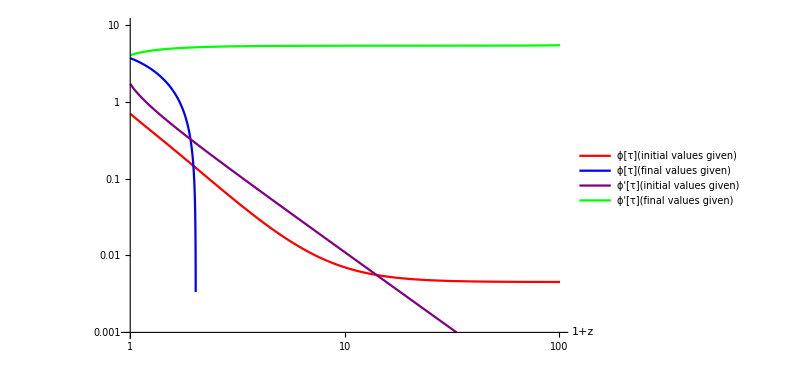

```mathematica
Show[Plotϕini,Plotϕfin,Plotϕprimeini,Plotϕprimefin]
```